```mathematica
Let's make a simple chain
```

a chain make s simple Let'

```mathematica
makeChain[n_] := Table[0, {i, n}]
```

```mathematica
chain = makeChain[20]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
makeEmptyIndexes[n_] :=  Table[i, {i,1, n}]
```

```mathematica
emptyIndexes = makeEmptyIndexes[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
DeleteCases[emptyIndexes, 2]
```

{1,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

### Example of how to fill up the chain

```mathematica
n = 0;
emptyIndexes = makeEmptyIndexes[20];
chain = makeChain[20];
While[Length[emptyIndexes] > 0, x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
chain[[x]] = RandomChoice[{-1, 1}]; n++; If[n == 5, Print[chain], n]];
Print[chain];
```

{0,0,1,-1,0,0,0,0,0,0,1,0,0,-1,0,1,0,0,0,0}

{-1,-1,1,-1,-1,-1,1,1,1,-1,1,1,-1,-1,-1,1,-1,-1,1,-1}

```mathematica
getChainIndexes[chain_] := Table[i, {i, Length[chain]}]
```

```mathematica
createNeighbours[node_] := {node - 1, node + 1}
```

```mathematica
inBoundaries[node_, N_] := node >= 1 && node ≤ N
```

```mathematica
findIsolatedClusters[chain_] := {isolatedClusterCount = 0; isolatedCount = 0;
howLong = Length[chain];
startNodes =getChainIndexes[chain];
visited={};
 toVisit = {};centers = {};
While[Length[startNodes] > 0 ,firstNode = Extract[startNodes,1]; startNodes = startNodes[[2;;]];
toVisit = Append[toVisit, firstNode];
currentType = chain[[firstNode]];
currentCount = 0; (* used to count how many members are in cluster if it's a cluster *)
fine = False;
While[Length[toVisit] > 0, node = Extract[toVisit, 1]; toVisit = toVisit[[2;;]];
nodeType = chain[[node]];
If[nodeType == 0,fine = True;, If[nodeType == currentType,
currentCount ++;visited = Append[visited, node]; startNodes = DeleteCases[startNodes, node]; neighbourNodes = createNeighbours[node];
neighbour1 = neighbourNodes[[1]];
neighbour2 = neighbourNodes[[2]];
If[inBoundaries[neighbour1, howLong], If[!MemberQ[visited, neighbour1], 
toVisit = Append[toVisit, neighbour1];], fine=True];
If[inBoundaries[neighbour2, howLong], If[!MemberQ[visited, neighbour2], toVisit = Append[toVisit, neighbour2];], fine=True];];];
];If[!fine, (*we found an isolated cluster *) isolatedClusterCount++; centers = Append[centers, firstNode]; isolatedCount = isolatedCount + currentCount;]];
{isolatedClusterCount, centers, isolatedCount}}
```

```mathematica
chain2 ={-1.,1.,1.,1.,-1.,1.,1.,-1.,-1.,1.}
```

{-1.,1.,1.,1.,-1.,1.,1.,-1.,-1.,1.}

```mathematica
chainExample ={1,1,-1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,-1,1,-1,1}
```

{1,1,-1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,-1,1,-1,1}

```mathematica
findIsolatedClusters[chainExample]
```

{{9,{3,4,10,11,13,14,17,18,19},17}}

### Other nice things that I learnt today

```mathematica
chainExample
```

{1,1,-1,1,1,1,1,1,1,-1,1,1,-1,1,1,1,-1,1,-1,1}

#### Pobieranie o określonym indeksie

```mathematica
node = Extract[chainExample, 1]
```

1

```mathematica
Length[chainExample]
```

20

#### Skracanie listy przez slajsing

```mathematica
chainExample[[2;;]]
```

{0,0,0,1,0,0,0,0,0,-1,1,-1,0,0,1,0,0,0,0}

```mathematica
myList = Append[{1, 2, 3}, 2]
```

{1,2,3,2}

```mathematica
x ={1,2}[[1]]
```

1

#### Usuwanie z listy konkretnego elementu / expression

```mathematica
DeleteCases[{1, 2, 3}, 5]
```

{1,2,3}

### A teraz razem, wypełnianie łańcucha i sprawdzanie clusterów :)

```mathematica
iter = 0;
maxLen = 50;
emptyIndexes = makeEmptyIndexes[maxLen];
chain = makeChain[maxLen];
While[Length[emptyIndexes] > 0, 

iter++;x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
chain[[x]] = RandomChoice[{-1, 1}]; 

clusters = findIsolatedClusters[chain];
If[clusters[[1, 1]] ≠ 0 && Mod[iter,10] == 0, Print["found after n: ", iter, " iterations; ", clusters]; Print[chain]; Print[emptyIndexes]]; ];
Print[chain];
```

found after n: 20 iterations; {{3,{13,14,15},3}}

{0,0,0,-1,0,0,0,0,1,0,0,-1,1,-1,1,-1,0,0,0,0,-1,0,1,0,1,0,0,1,-1,0,0,0,0,1,-1,0,1,1,0,0,1,0,0,0,0,-1,0,-1,-1,0}

{1,2,3,5,6,7,8,10,11,17,18,19,20,22,24,26,27,30,31,32,33,36,39,40,42,43,44,45,47,50}

found after n: 30 iterations; {{4,{13,14,15,29},5}}

{-1,-1,0,-1,-1,0,0,0,1,0,0,-1,1,-1,1,-1,0,-1,-1,0,-1,-1,1,0,1,0,1,1,-1,-1,1,0,0,1,-1,0,1,1,0,0,1,0,0,0,0,-1,0,-1,-1,1}

{3,6,7,8,10,11,17,20,24,26,32,33,36,39,40,42,43,44,45,47}

found after n: 40 iterations; {{11,{13,14,15,23,24,29,31,32,34,47,48},14}}

{-1,-1,0,-1,-1,-1,0,1,1,1,0,-1,1,-1,1,-1,0,-1,-1,0,-1,-1,1,-1,1,0,1,1,-1,-1,1,-1,-1,1,-1,0,1,1,0,1,1,0,1,1,0,-1,1,-1,-1,1}

{3,7,11,17,20,26,36,39,42,45}

found after n: 50 iterations; {{24,{8,11,13,14,15,16,23,24,25,26,27,29,31,32,34,35,37,39,40,42,43,46,47,48},42}}

{-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,-1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,1,1,1,-1,1,-1,-1,1}

{}

{-1,-1,-1,-1,-1,-1,-1,1,1,1,-1,-1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,1,-1,1,-1,1,1,-1,-1,1,-1,-1,1,-1,-1,1,1,-1,1,1,-1,1,1,1,-1,1,-1,-1,1}

```mathematica
simulateChain[maxLength_, types_:2] := Module[{maxLen = maxLength, isolatedCountArray, notIsolatedCountArray, emptyIndexes, chain, iter}, iter = 0;
isolatedCountArray = {};
notIsolatedCountArray = {};
emptyIndexes = makeEmptyIndexes[maxLen];
chain = makeChain[maxLen];
While[Length[emptyIndexes] > 0, 
iter++;
(* fill the random empty place with random type *)
x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
chain[[x]] = RandomChoice[Table[i, {i, 1, types}]]; 

clusters = findIsolatedClusters[chain];
isolated = clusters[[1, 3]];

isolatedCountArray = Append[isolatedCountArray, isolated];
notIsolatedCountArray = Append[notIsolatedCountArray, iter - isolated];];
{notIsolatedCountArray, isolatedCountArray}]
```

```mathematica
maxLen = 100;
countsArray = simulateChain[maxLen];
```

```mathematica
TODO :
- dopasować wzrost Z = t ^ 3 / (4 N ^ 2) (more less fine)
- wyliczyć tc (ok)
- zebrać statystykę dla Tc (ok)
- narysować wykresy  w stylu Fig 2 (ok)
- zgeneralizować wyniki do m > 2 i narysować tego wykresy
- dwu wymiarowa siatka
- grafy?
```

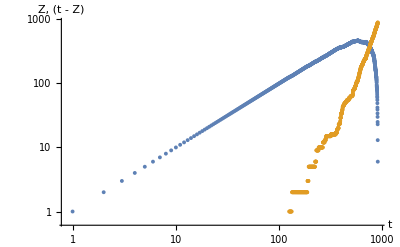

```mathematica
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
maxLen = 100;

For[i=0,i<20,i++,countsArray = simulateChain[maxLen, 2];Z = countsArray[[2]];
Clear[x];
qp = ListPlot[Z];
fit = Fit[Z, { 1 ,x, x^2,  x^3}, x ];
]
```

```mathematica
1.0 / (4 * maxLen ^2)
```

0.000025

```mathematica
allTCs = {};
allMeanTCs = {};
maxLens = {};
```

```mathematica
allTCs = {};
allMeanTCs = {};
maxLens = {};
For[g= 100, g < 1000,g+= 100,
For[i=0,i<10,i++,countsArray = simulateChain[g, 2];Z = countsArray[[2]];
Clear[x];
tC = Length@First@Split[Z,#1==0&];
allTCs = Append[allTCs, tC];
];
maxLens = Append[maxLens, g];
allMeanTCs = Append[allMeanTCs, Mean[allTCs]];
allTCs = {};
Print["All for maxLen ", g, " are ready"]; 
];
```

```mathematica
data = Transpose[{maxLens,allMeanTCs}]
```

{{100,138/5},{200,212/5},{300,593/10},{400,701/10},{500,957/10},{600,571/5},{700,1157/10},{800,1131/10},{900,774/5}}

```mathematica
N[2^(2/3)]
```

1.5874

```mathematica
fit = Fit[data, { x ^ (2 / 3)}, x]
```

1.47455 x^(2/3)

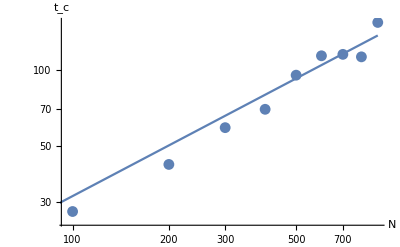

```mathematica
Show[ListLogLogPlot[data], LogLogPlot[fit, {x,1, 900}], AxesLabel -> {"N", "t_c"}]
```

```mathematica
Transpose
Transpose[{{a,b,c,d},{1,2,3,4}}]
```

```mathematica
countsArray[[2]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,6,6,6,6,6,7,7,7,7,9,9,17,17,17,17,17,20,20,25,25,25,25,29,30,30,35,35,38,38,45,50,50,50,53,55,58,58,62,65,70,70,78,85,94}

```mathematica
Length@First@Split[Z,#1==0&]
```

35

```mathematica
Greater
```

Greater

```mathematica
tExpected = (2 * maxLen) ^ (2 / 3)
```

20 5^(1/3)

```mathematica
N[tExpected]
```

34.1995

```mathematica
N[Mean[allTCs]]
```

31.3368

```mathematica
Mean[{{1, 2, 3}, {2, 3, 4}}]
```

{3/2,5/2,7/2}

```mathematica
Table[i, {i, 1, 3}]
```

{1,2,3}

```mathematica
getZAndRest[maxLen_, types_:2] := Module[{allZ, allRest, i},
allZ = {};
allRest = {};
For[i=0,i<10,i++,countsArray = simulateChain[maxLen, types];Z = countsArray[[2]];
allZ = Append[allZ, Z];
allRest = Append[allRest, countsArray[[1]]];
];
meanZ = Mean[allZ];
meanRest = Mean[allRest];
{meanZ, meanRest} ]

Blah data for analysis
```

```mathematica
{meanZ100, meanRest100} = getZAndRest[100];
{meanZ200, meanRest200} = getZAndRest[200];
```

```mathematica
{meanZ300, meanRest300} = getZAndRest[300];
{meanZ400, meanRest400} = getZAndRest[400];
```

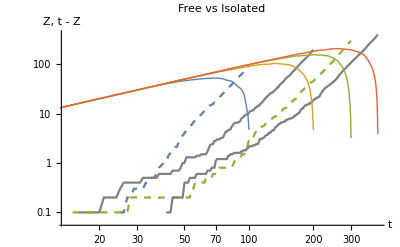

```mathematica
Show[ListLogLogPlot[{meanZ100, meanZ200, meanZ300, meanZ400}, PlotStyle->{Dashed, Gray}, Joined->True], ListLogLogPlot[{meanRest100, meanRest200, meanRest300, meanRest400}, PlotStyle->Thick, Joined->True] , AxesLabel->{HoldForm[t],HoldForm["Z, t - Z"]},PlotLabel->HoldForm[Free vs Isolated]]
```

```mathematica
allTCs = {};
allMeanTCs = {};
allTypes = {};
maxLen = 1000;
For[g =2, g <= 8, g *= 2,
For[i=0,i<2,i++,countsArray = simulateChain[maxLen, g];Z = countsArray[[2]];
tC = Length@First@Split[Z,#1==0&];
allTCs = Append[allTCs, tC];
];
allTypes = Append[allTypes, g];
allMeanTCs = Append[allMeanTCs, Mean[allTCs]];
allTCs = {};
Print["All for types ", g, " are ready"]; 
];
```

All for types 2 are ready

All for types 4 are ready

All for types 8 are ready

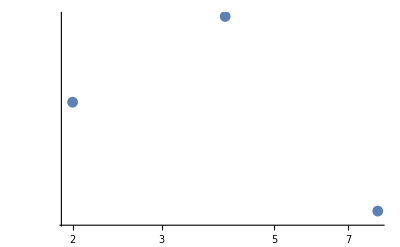

```mathematica
ListLogLogPlot[Transpose[{allTypes, allMeanTCs}]]
```